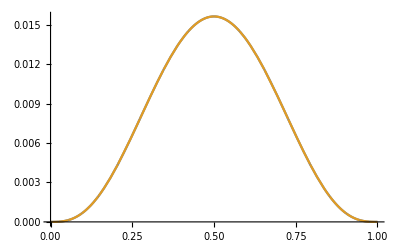

```mathematica
(*
 Функцията f(t), за която се търси естествен кубичен сплайн, начална стойност на n, и степента на сплайна r
(в случая r=3, тъй като търсим кубичен сплайн)
*)
(*Брой възли*)
n=20;
(*функцията,която ще бъде интерполирана от търсения естествен кубичен сплайн*)
f[t_]:=t^3*(1-t)^3;
(*Инициализация на възлите в[0,1]*)
Do[x[k]=(Sin[(k*Pi)/(2*n)])^2,{k,1,n-1}];
x[0]=0;
x[n]=1;
(*пресмятаме разстоянието между всеки два съседни възела*)
Do[h[k]=x[k+1]-x[k],{k,0,n-1}]; 
(*Дефиниране на коефизиентите в тридиагоналната матрица*)
Do[a[k]=1/h[k-1],{k,2,n-1}];
Do[b[k]=2/h[k-1]+2/h[k],{k,1,n-1}];
Do[c[k]=1/h[k],{k,1,n-2}];
(* Дефинираме десните страни на уравненията в тридиагоналната матрица *)
Do[value[k]=3*(f[x[k]]-f[x[k-1]])/h[k-1]^2+3*(f[x[k+1]]-f[x[k]])/h[k]^2,{k,1,n-1}];
(*Начална инициализация на α1 и β1*)
alpha[1]=-c[1]/b[1];
beta[1]=value[1]/b[1];
(*Прав ход на прогонката*)
Do[alpha[k]=-c[k]/(a[k]*alpha[k-1]+b[k]),{k,2,n-1}];
Do[beta[k]=(value[k]-a[k]*beta[k-1])/(a[k]*alpha[k-1]+b[k]),{k,2,n-1}];
(* Метод на прогонката - обратен ход *)
d[0]=f'[x[0]];
d[n]=f'[x[n]];
Do[d[k]=alpha[k]*d[k+1]+beta[k],{k,n-1,1,-1}];

(*pk(x)=sn(x) x={xk,xk+1} - oбщ вид на полиномите интерполиращи f(t) във всеки подинтервал на [0, 1],определен от два последователни интерполационни възела *)
P[k_,t_]:=f[x[k]]+d[k]*(t-x[k])+(((f[x[k+1]]-f[x[k]])/h[k]-d[k])/h[k])*(t-x[k])^2+((d[k+1]-2*(f[x[k+1]]-f[x[k]])/h[k]+d[k])/h[k]^2)*(t-x[k])^2*(t-x[k+1]);
(*Сплайн функцията *)
S[t_]:=Sum[If[t≥x[k]&&t≤x[k+1],P[k,t],0],{k,0,n-1}];

(* Едновременно визуализиране на графиките на f[t] и Sn[t] в интервала [0,1] *)
Plot[{f[t],S[t]},{t,0,1},PlotRange->All] 
(*Визуализация на f(t)-sn(t) в [0,1]-грешката*)
Plot[f[t]-S[t],{t,0,1}, PlotRange->All]
```

```mathematica
20
```

20

Plot::nonopt: Options expected (instead of PlotRange→All) beyond position 2 in Plot[{f[t],S[t]},{t,0,1},PlotRange→All]. An option must be a rule or a list of rules.

Plot[{f[t],S[t]},{t,0,1},PlotRange→All]